11

{{38,62,0,0,0,0,0,0,0,0,0,0},{19,20,28,34,0,0,0,0,0,0,0,0},{11,13,15,10,30,22,0,0,0,0,0,0},{6,12,8,11,5,23,15,19,0,0,0,0},{4,10,8,8,9,3,13,20,8,17,0,0},{3,8,8,5,7,7,3,7,18,12,6,15}}

{100,101,101,99,100,99}

0.01822 (2-Cos[t]+Sin[t]+t Sin[t]^2+Sin[t]^11)

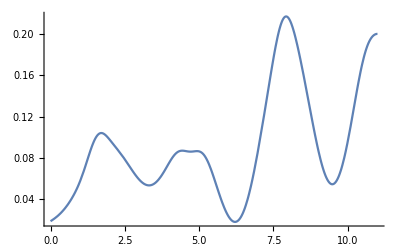

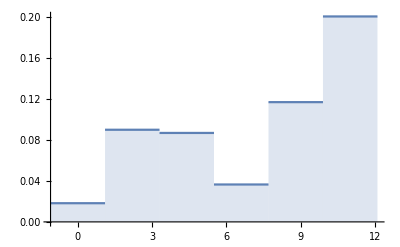

```mathematica
T=RandomInteger[{1,20}]
stake =100;
f[x_] = (x*Sin[x]^2+D[Cos[x],{x,T}]+D[Sin[x],{x,T}]+Sin[x]^T+2);
F[x_] = f[t]/NIntegrate[f[t],{t,0,T}];
S = Table[Table[Round[stake*NIntegrate[F[t],{t,i*T/rounds,(i+1)*T/rounds}]],{i,0,rounds-1}],{rounds,2,12,2}];
padS = Table[PadRight[Part[S,i],12],{i,1,6}]
check=Table[Sum[Part[padS,i,j],{j,1,Length[Part[S,i]]}],{i,1,6}]
F[x]
Plot[F[t],{t,0,T},PlotRange->Full ]
DiscretePlot[F[t],{t,0,T, T/(6-1)},ExtentSize->Full,ExtentMarkers->None]
```